```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->8]
```

## Aufgabe 3

```mathematica
data30=309.2
```

309.2

```mathematica
data3={{291.5,266.5},{328.8,351.3}}
```

{{291.5,266.5},{328.8,351.3}}

```mathematica
data3processed=Table[(data3[[2,i]]-data3[[1,i]])/2,{i,1,2}]
```

{18.65,42.4}

```mathematica
(0.1)/Sqrt[2]
```

0.0707107

```mathematica
data3radians=data3processed*2Pi/360
```

{0.325504,0.74002}

```mathematica
data3processed Degree
```

{0.325504,0.74002}

```mathematica
0.1/(√2) *2Pi/360
```

0.00123413

```mathematica
data3sines=Sin[#]&/@data3radians
```

{0.319786,0.674302}

```mathematica
data3sineserror=Cos[#]*0.1/(√2) *2Pi/360&/@data3radians
```

{0.00116933,0.000911353}

```mathematica
data3sines/(0.1/40)
```

{127.915,269.721}

```mathematica
data3sineserror/(0.1/40)
```

{0.467732,0.364541}

```mathematica
b3=data3sines[[2]]-data3sines[[1]]
```

0.354516

```mathematica
Δb3=√Total[(#1^2&)/@data3sineserror]
```

0.00148253

```mathematica
g=589/b3
Δg=589/(b3^2)Δb3
```

1661.42

6.94779

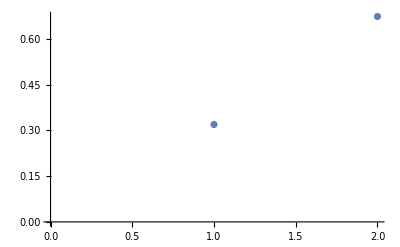

```mathematica
ListPlot[Sin[# Degree]&/@data3processed]
```

```mathematica
Sin[data3processed[[2]]Degree]-Sin[data3processed[[1]]Degree]
```

0.354516

## Aufgabe 5

```mathematica
data50=126.3
data5={{71.8,86.4,97.3,91.3},{172.1,164.0,155.6,160.9}}
```

126.3

{{71.8,86.4,97.3,91.3},{172.1,164.,155.6,160.9}}

```mathematica
data5processed=(#[[2]]-#[[1]])/2&/@Transpose[data5]
```

{50.15,38.8,29.15,34.8}

```mathematica
data5rad=data5processed*2Pi/360
```

{0.875283,0.677188,0.508763,0.607375}

```mathematica
0.1/(√2)
0.1/(√2) *2Pi/360
```

0.0707107

0.00123413

```mathematica
data5sines=Sin[#]&/@data5rad
```

{0.767725,0.626604,0.487098,0.570714}

```mathematica
data5sineserror=Abs[Cos[#]](0.1/(√2) *2Pi/360)&/@data5rad
```

{0.000790808,0.000961808,0.00107783,0.00101341}

```mathematica
g #/2 &/@data5sines
```

{637.756,520.526,404.637,474.097}

```mathematica
Table[1/2 Sqrt[(data5sines[[i]])^2 Δg^2 + g^2 data5sineserror[[i]]^2],{i,1,Length[data5sines]}]
```

{2.74671,2.31876,1.91441,2.15393}

## Aufgabe 6

```mathematica
266.3-146.3
```

120.

```mathematica
0.1/Sqrt[2]
```

0.0707107

## Aufgabe 7

```mathematica
cf=ColorData["VisibleSpectrum"]
```

ColorDataFunction[…]

```mathematica
D[Sin[(ϵ+δmin)/2]/Sin[ϵ/2], δmin]
```

1/2 Cos[(δmin+ϵ)/2] Csc[ϵ/2]

```mathematica
wavelengths={643.9,579.1,546.1,508.6,480.0,467.8,435.8,404.7}
```

{643.9,579.1,546.1,508.6,480.,467.8,435.8,404.7}

```mathematica
cf/@wavelengths
```

{RGBColor[0.9672897238016622, 0., 0.],RGBColor[1., 0.9016450639686833, 0.],RGBColor[0., 1., 0.],RGBColor[0., 0.9743380178113661, 0.4033040430876886],RGBColor[0., 0.48449418286510887, 1.],RGBColor[0., 0.09872836549392221, 1.],RGBColor[0.47842342393879017, 0., 1.],RGBColor[0.23437896046341472, 0., 0.4939999999999998]}

```mathematica
ϵ=Pi/3
```

π/3

```mathematica
Δδmin=Sqrt[2]*0.1
```

0.141421

```mathematica
n[δmin_]:=Sin[(ϵ+δmin)/2]/Sin[ϵ/2]
```

```mathematica
Δn[δmin_]:=Cos[(ϵ+δmin)/2]/(2Sin[ϵ/2])Δδmin
```

```mathematica
ethylcinnamat={131,131.7,132.2,132.9,133.6,134.0,135.2}-102.5
```

{28.5,29.2,29.7,30.4,31.1,31.5,32.7}

```mathematica
flintglas={145.7,146.3,146.6,146.9,147.5,147.8,148.5,149.4}-98
```

{47.7,48.3,48.6,48.9,49.5,49.8,50.5,51.4}

```mathematica
schwerflintglas={138.0,138.8,139.3,140.2,140.8,141.3,142.5,144.2}-79.1
```

{58.9,59.7,60.2,61.1,61.7,62.2,63.4,65.1}

```mathematica
ethylcinnamatrad=ethylcinnamat Degree
flintglasrad = flintglas Degree
schwerflintglasrad = schwerflintglas Degree
```

{0.497419,0.509636,0.518363,0.53058,0.542797,0.549779,0.570723}

{0.832522,0.842994,0.84823,0.853466,0.863938,0.869174,0.881391,0.897099}

{1.028,1.04196,1.05069,1.0664,1.07687,1.08559,1.10654,1.13621}

```mathematica
Sqrt[2]*0.1*2Pi/360
```

0.00246827

```mathematica
ethn=n/@ethylcinnamatrad
fglasn=n/@ flintglasrad
sflintglasn=n/@ schwerflintglasrad
```

{1.39558,1.40431,1.41051,1.41914,1.42772,1.4326,1.44714}

{1.61495,1.62111,1.62417,1.62722,1.63328,1.6363,1.64329,1.6522}

{1.72237,1.72943,1.73379,1.74157,1.74669,1.75093,1.76095,1.77483}

```mathematica
ethdn=Δn/@ethylcinnamatrad
fglasdn=Δn/@ flintglasrad
sflintglasdn=Δn/@ schwerflintglasrad
```

{0.1013,0.100696,0.100261,0.0996503,0.0990355,0.0986825,0.0976163}

{0.0834246,0.0828256,0.0825252,0.0822242,0.0816207,0.081318,0.0806097,0.0796946}

{0.0718831,0.0710311,0.0704968,0.0695318,0.068886,0.0683465,0.0670462,0.0651916}

```mathematica
tabeth=Join[Riffle[Around[#,Sqrt[2]*0.1*2Pi/360]&/@ethylcinnamatrad,Table[Around[ethn[[i]],ethdn[[i]]],{i,1,Length[ethn]}]],{0,0}]
tabfglas=Riffle[Around[#,Sqrt[2]*0.1*2Pi/360]&/@flintglasrad,Table[Around[fglasn[[i]],fglasdn[[i]]],{i,1,Length[fglasn]}]]
tabsflintglas=Riffle[Around[#,Sqrt[2]*0.1*2Pi/360]&/@schwerflintglasrad,Table[Around[sflintglasn[[i]],sflintglasdn[[i]]],{i,1,Length[sflintglasn]}]]
```

{0.49740.0025,1.400.10,0.50960.0025,1.400.10,0.51840.0025,1.410.10,0.53060.0025,1.420.10,0.54280.0025,1.430.10,0.54980.0025,1.430.10,0.57070.0025,1.450.10,0,0}

{0.83250.0025,1.610.08,0.84300.0025,1.620.08,0.84820.0025,1.620.08,0.85350.0025,1.630.08,0.86390.0025,1.630.08,0.86920.0025,1.640.08,0.88140.0025,1.640.08,0.89710.0025,1.650.08}

{1.02800.0025,1.720.07,1.04200.0025,1.730.07,1.05070.0025,1.730.07,1.06640.0025,1.740.07,1.07690.0025,1.750.07,1.08560.0025,1.750.07,1.10650.0025,1.760.07,1.13620.0025,1.770.07}

```mathematica
labels=Riffle[{"λ_1","λ_2","λ_4","λ_5","λ_6","λ_7","λ_8","λ_9"},{"n(λ_1)","n(λ_2)","n(λ_4)","n(λ_5)","n(λ_6)","n(λ_7)","n(λ_8)","n(λ_9)"}]
```

{λ_1,n(λ_1),λ_2,n(λ_2),λ_4,n(λ_4),λ_5,n(λ_5),λ_6,n(λ_6),λ_7,n(λ_7),λ_8,n(λ_8),λ_9,n(λ_9)}

```mathematica
TeXForm[Transpose[{labels,tabeth,tabfglas,tabsflintglas}]]//CopyToClipboard
```

```mathematica
Length/@{tabeth,tabfglas,tabsflintglas}
```

{16,16,16}

```mathematica
schwerflintglasint=Interpolation[Transpose[{wavelengths,schwerflintglas}],InterpolationOrder->Automatic]
```

InterpolatingFunction[…]

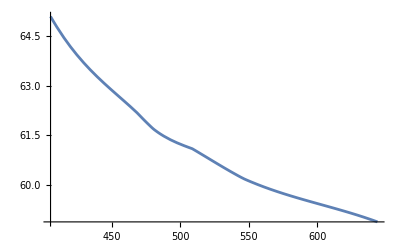

```mathematica
Plot[schwerflintglasint[x],{x,405,644}]
```

```mathematica
wavelengths
```

{643.9,579.1,546.1,508.6,480.,467.8,435.8,404.7}

### Plot Ethylcinnamat

```mathematica
(650-wavelengths)
```

{6.1,70.9,103.9,141.4,170.,182.2,214.2,245.3}

```mathematica
wavelengths
```

{643.9,579.1,546.1,508.6,480.,467.8,435.8,404.7}

```mathematica
(ethylcinnamatrad-0.49)*20/0.01
```

{14.8377,39.2723,56.7256,81.1602,105.595,119.557,161.445}

```mathematica
ethylcinnamatrad[[-1]]-ethylcinnamatrad[[1]]
```

0.0733038

```mathematica
Sqrt[2]*0.1*2Pi/360*20/0.01
```

4.93654

```mathematica
Print/@Transpose[{(650-wavelengths[[1;;-2]]),(ethylcinnamatrad-0.49)*20/0.01 }];
```

{6.1,14.8377}

{70.9,39.2723}

{103.9,56.7256}

{141.4,81.1602}

{170.,105.595}

{182.2,119.557}

{214.2,161.445}

### Plot Flintglas

```mathematica
(650-wavelengths)
```

{6.1,70.9,103.9,141.4,170.,182.2,214.2,245.3}

```mathematica
flintglasrad
```

{0.832522,0.842994,0.84823,0.853466,0.863938,0.869174,0.881391,0.897099}

```mathematica
(flintglasrad-0.83)*20/0.01
```

{5.04411,25.9881,36.46,46.932,67.876,78.3479,102.783,134.198}

```mathematica
Print/@Transpose[{(650-wavelengths),(flintglasrad-0.83)*20/0.01}];
Sqrt[2]*0.1*2Pi/360*20/0.01
```

{6.1,5.04411}

{70.9,25.9881}

{103.9,36.46}

{141.4,46.932}

{170.,67.876}

{182.2,78.3479}

{214.2,102.783}

{245.3,134.198}

4.93654

### Plot Schwerflintglas

```mathematica
schwerflintglasrad
```

{1.028,1.04196,1.05069,1.0664,1.07687,1.08559,1.10654,1.13621}

```mathematica
(650-wavelengths)*10/20
```

{3.05,35.45,51.95,70.7,85.,91.1,107.1,122.65}

```mathematica
(schwerflintglasrad-1.02)*20/0.01
```

{15.9979,43.9231,61.3764,92.7923,113.736,131.19,173.077,232.419}

```mathematica
Print/@Transpose[{(650-wavelengths)*10/20,(schwerflintglasrad-1.02)*20/0.01}];
```

{3.05,15.9979}

{35.45,43.9231}

{51.95,61.3764}

{70.7,92.7923}

{85.,113.736}

{91.1,131.19}

{107.1,173.077}

{122.65,232.419}

### Brechzahldifferenz

```mathematica
fglasn[[8]]-fglasn[[4]]
Sqrt[fglasdn[[4]]^2+fglasdn[[8]]^2]
sflintglasn[[8]]-sflintglasn[[4]]
Sqrt[sflintglasdn[[4]]^2+sflintglasdn[[8]]^2]
```

0.0249797

0.114508

0.0332567

0.0953132

```mathematica
ethn[[7]]-ethn[[4]]
Sqrt[ethdn[[4]]^2+ethdn[[7]]^2]
```

0.0279981

0.139496

## Aufgabe 9

```mathematica
data9=({140.6,139.9,142.2}-81)Degree//N
```

{1.04022,1.028,1.06814}

```mathematica
Sqrt[2]*0.1*2Pi/360
```

0.00246827

```mathematica
(data9-1.02)*20/0.01
```

{40.4325,15.9979,96.283}

```mathematica
schwerflintglas
```

{58.9,59.7,60.2,61.1,61.7,62.2,63.4,65.1}

```mathematica
139.9-81
```

58.9

## Aufgabe 10.1

```mathematica
data10={140.6,139.9,142.2}-81.0
```

{59.6,58.9,61.2}

```mathematica
Values[Solve[schwerflintglasint[x]==#1,x]]&/@data10
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{{587.228}},{{643.9}},{{502.079}}}

```mathematica
FindRoot[schwerflintglas[x]-data10[[1]],{x,500}]
```

FindRoot::nlnum: The function value {-59.6+{58.9,59.7,60.2,61.1,61.7,62.2,63.4,65.1}[500.]} is not a list of numbers with dimensions {1} at {x} = {500.}.

FindRoot[schwerflintglas[x]-data10⟦1⟧,{x,500}]

```mathematica
ListPlot[]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[]

```mathematica
140-81
```

59

```mathematica
59+79.1
```

138.1

```mathematica
579.1/(579.1-577.0)
```

275.762

```mathematica
577.0/(579.1-577.0)
```

274.762

## Theoretische Auflösungsvermögen

```mathematica
D[]
```

D::argm: D called with 0 arguments; 1 or more arguments are expected.

D[]

```mathematica
D[(y2-y1)/(x2-x1),{{x1,x2,y1,y2}}]
```

D::ivar: {22,23,20} is not a valid variable.

∂_{{{22,23,20},{9000,8000,6000},{0.023,0.021,0.017},{8,7.5,6}}} {0.000888505,0.000937571,0.0010005}

```mathematica
y2=1.085;
y1=1.0225;
x1=648*10^(-9);
x2=438*10^(-9);
```

```mathematica
0.01/20
```

0.0005

```mathematica
Δx=2*10^(-9);
Δy=0.0005
```

0.0005

```mathematica
steigung=(y2-y1)/(x2-x1)
```

-297619.

```mathematica
dsteigung=Sqrt[((-y1+y2)/(-x1+x2)^2)^2 (2(Δx)^2)+(1/(-x1+x2))^2 (2 (Δy)^2)]
```

5235.1

```mathematica
steigung=(1.085-1.0225)/((648-438)/10^9)
```

297619.

```mathematica
dmin=(81.45-80.06)*10^(-3)
```

0.00139

```mathematica
ddmin=Sqrt[(0.01)^2+(0.01)^2]*10^(-3)
```

0.0000141421

```mathematica
dmin Abs@steigung
```

413.69

```mathematica
Sqrt[steigung^2 ddmin^2 + dmin^2 dsteigung^2]
```

8.40637

```mathematica
(81.45-80.06)
Sqrt[(0.01)^2+(0.01)^2]
```

1.39

0.0141421

```mathematica
steigung*(81.45-80.06)*10^(-3)
```

413.69